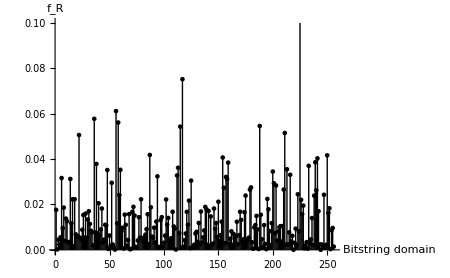

```mathematica
(*Generate example data*)
n=2^8;
data=RandomVariate[ExponentialDistribution[80],n];  (*small positive values*)

ListPlot[data,Filling->Axis,PlotStyle->Black,FillingStyle->Black,PlotRange->{0,0.1},AxesLabel->{Style["Bitstring domain",14],Style[Subscript[f,R],14]},ImageSize->450,AxesStyle->Directive[Black,12],PlotRangePadding->None,Ticks->None]
```

```mathematica
k=50;
arr=ConstantArray[0,n];
arr[[RandomSample[Range[n],k]]]=1;
```

```mathematica
samp = arr*data;
```

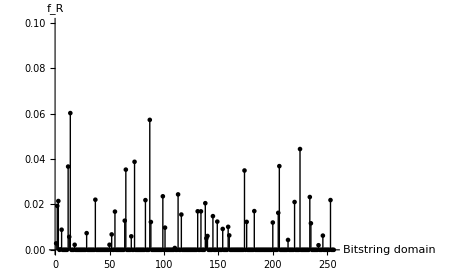

```mathematica
ListPlot[samp,Filling->Axis,PlotStyle->Black,FillingStyle->Black,PlotRange->{0,0.1},AxesLabel->{Style["Bitstring domain",14],Style[Subscript[f,R],14]},ImageSize->450,AxesStyle->Directive[Black,12],PlotRangePadding->None,Ticks->None]
```

```mathematica
Thresh[arr_,t_]:=UnitStep[arr-t]*arr
```

```mathematica
threshSamp = Thresh[samp,0.02];
```

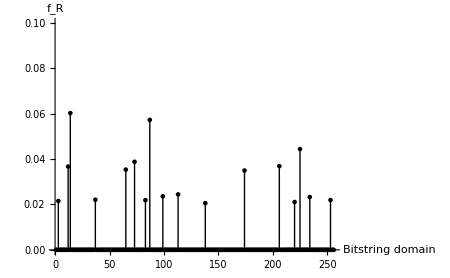

```mathematica
ListPlot[threshSamp,Filling->Axis,PlotStyle->Black,FillingStyle->Black,PlotRange->{0,0.1},AxesLabel->{Style["Bitstring domain",14],Style[Subscript[f,R],14]},ImageSize->450,AxesStyle->Directive[Black,12],PlotRangePadding->None, Ticks->None]
```

```mathematica
Id := IdentityMatrix[2]
Zero:={{1,0},{0,0}}
One:={{0,0},{0,1}}
Unprotect[CircleTimes];
ClearAll[CircleTimes];
SetAttributes[CircleTimes,Flat];
CircleTimes[args__]:=KroneckerProduct[args];
Protect[CircleTimes];
```

```mathematica
m=8;

ops={Zero,One};

(*build all pairs of bit positions*)
pairs=Subsets[Range[m],{2}];

(*build matrices*)
Ma=Flatten[Table[Module[{pattern},pattern=ConstantArray[Id,m];
pattern[[pairs[[p,1]]]]=ops[[a]];
pattern[[pairs[[p,2]]]]=ops[[b]];
Diagonal@@{Apply[CircleTimes,pattern]}],{p,Length[pairs]},{a,2},{b,2}],2];

M=Normalize/@Transpose[Ma];
M=Transpose[M];
```

```mathematica
ArrayPlot[M,ColorRules->{0->White,1->GrayLevel[0]},Frame->True,FrameStyle->Black,ImageSize->600]
```

-Graphics-

```mathematica
y = M.threshSamp;
```

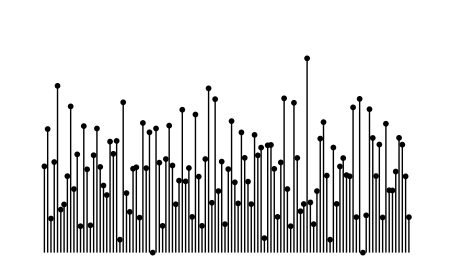

```mathematica
Rotate[ListPlot[y,Filling->Axis,PlotStyle->Black,FillingStyle->Black,PlotRange->{0,0.07},Axes->False,ImageSize->450,AxesStyle->Directive[Black,12],PlotRangePadding->None, Ticks->None],-Pi/2]
```

```mathematica
KeepKLargest[arr_,k_]:=Module[{t},t=Part[Sort[arr],-k];
arr*UnitStep[arr-t]]
```

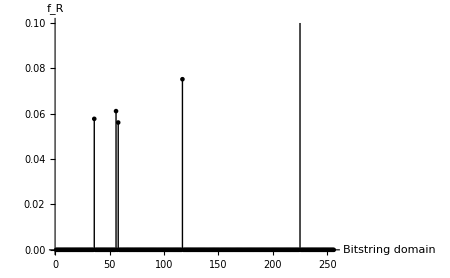

```mathematica
ListPlot[KeepKLargest[data,5],Filling->Axis,PlotStyle->Black,FillingStyle->Black,PlotRange->{0,0.1},AxesLabel->{Style["Bitstring domain",14],Style[Subscript[f,R],14]},ImageSize->450,AxesStyle->Directive[Black,12],PlotRangePadding->None, Ticks->None]
```